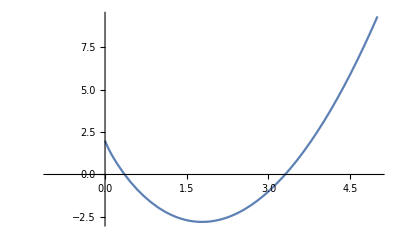

```mathematica
f[x_] = x Log[3,x]+x^2-5 x+2;
Plot[f[x], {x, -1, 5}]
```

```mathematica
solutions = Solve[f[x] == 0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[2-5 x+x^2+(x Log[x])/Log[3]==0,x]

```mathematica
solutions = NSolve[f[x] == 0,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[2-5 x+x^2+(x Log[x])/Log[3]==0,x]

```mathematica
solutions = FindRoot[f[x]==0,{x,1}]
solutions = FindRoot[f[x]==0,{x,2}]
```

{x→0.358796}

{x→3.30658}